N/500000

e1:t:1. and is N

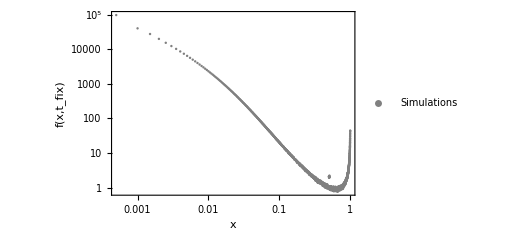

```mathematica
N1=1000;
mu=10^-6;
L=10000;
theta=4 N1 mu L;(theta=2 N mu)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/average_data_high_CI_decided_s_0.1.txt"];

datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x21s};

a1s=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","\!\(\*
StyleBox[\"f\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\"(\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\"x\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\",\",\nFontSlant->\"Italic\"]\)\!\(\*SubscriptBox[
StyleBox[\"t\",\nFontSlant->\"Italic\"], \(fix\)]\)\!\(\*
StyleBox[\")\",\nFontSlant->\"Italic\"]\)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray},PlotLegends->{"Simulations","Diffusion"}];
a2s=LogLogPlot[theta/x,{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]}];
a3s=LogLogPlot[theta/(88.18855784893822 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]}];

Show[a1s,a2s,a3s,PlotRange->All]
```

```mathematica
N1=1000;
mu=10^-6;
L=10000;
theta=4 N1 mu L;
```

```mathematica
theta
```

40

```mathematica
Quit[]
```

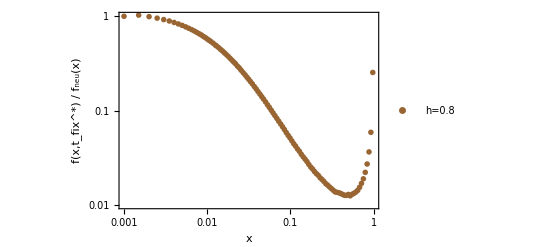

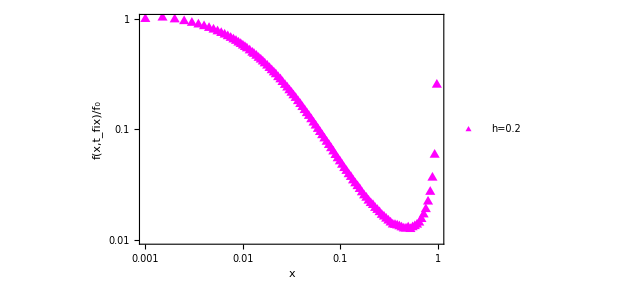

```mathematica
N1=1000;
mu=10^-6;
L=10000;
theta=4 N1 mu L;
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/average_data_high_CI_decided_s_0.1.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1s=Transpose@{x11s,x11s x21s/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium, FontSize->16],PlotStyle->{Brown},PlotLegends->{""},PlotRange->{{0.001,1},{0.01,1}}, PlotMarkers->{"♣",12}];
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
Brown},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.01,1}}, PlotMarkers->{"♣",12}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t",Italic],Style["fix",Italic],"*"]//DisplayForm,Style[") / ",Italic],SubscriptBox[Style["f",Italic],"StyleBox[\"neu\",FontSlant->\"Italic\"]"]//DisplayForm,Style["(x)",Italic]}]]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
Brown},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.01,1}}, PlotMarkers->{"♣",12}];



(*Show both plots*)
Show[a1sCombined]
```

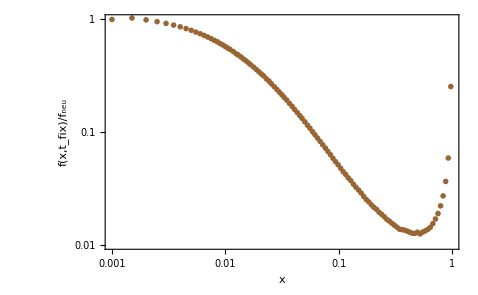
```mathematica
a1=-Graphics-;
```

```mathematica
Data1s
```

{{0.,0.},{0.0005,(2.40851×10^7)/N},{0.001,(1.99197×10^7)/N},{0.0015,(2.05091×10^7)/N},{0.002,(1.97551×10^7)/N},{0.0025,(1.90366×10^7)/N},{0.003,(1.83839×10^7)/N},{0.0035,(1.77595×10^7)/N},{0.004,(1.71392×10^7)/N},{0.0045,(1.65308×10^7)/N},{0.005,(1.59631×10^7)/N},1979,{0.995,(1.19052×10^7)/N},{0.9955,(1.2793×10^7)/N},{0.996,(1.33498×10^7)/N},{0.9965,(1.4759×10^7)/N},{0.997,(1.56506×10^7)/N},{0.9975,(1.72261×10^7)/N},{0.998,(1.84026×10^7)/N},{0.9985,(2.01529×10^7)/N},{0.999,(2.1665×10^7)/N},{0.9995,(2.1975×10^7)/N},{1.,0.}}
 |  |  |  |

```mathematica
Quit[]
```

```mathematica
N1 = 1000;
mu = 10^-6;
L = 10/100 1000;
theta = 4 N1 mu L
h = 0.5;
```

2/5

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

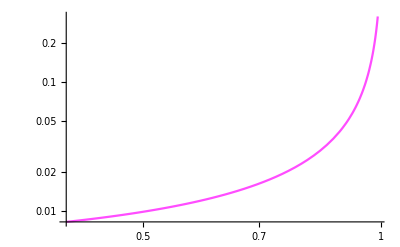

```mathematica
N1 = 1000;
mu = 10^-6;
L = 10/100 1000;
theta = 4 N1 mu L; 
h = 0.5;
(*s=0.1;*)


b = LogLogPlot[{1/2  x/40. NIntegrate[ 10 Exp[-10 s] (theta ⅇ^(2 N1 s ((1-2 h)x^2 + 2 h x )) ∫_x^1 ⅇ^(-2 N1 s ( (1-2 h) y^2 + 2 h y ))ⅆy)/(x (1-x) ∫_0^1 ⅇ^(-2 N1 s ( (1- 2h) y^2 + 2 h y))ⅆy), {s,0,Infinity}] }, {x,0.4,0.99}, PlotStyle->Lighter[Magenta, 0.3]]
```

```mathematica
a2=-Graphics-;
```

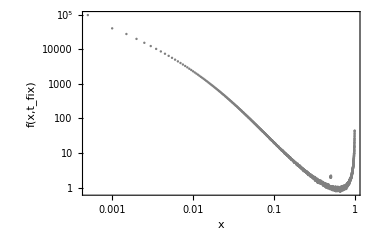
```mathematica
a1=-Graphics-;
```

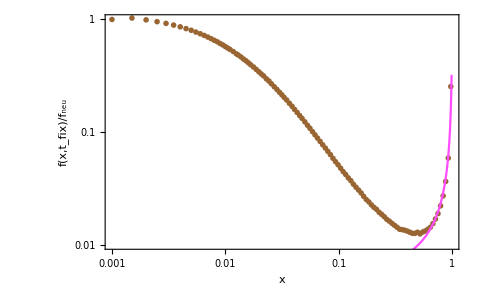

```mathematica
Show[a1,a2]
```

```mathematica
f1=-Graphics-;
```

```mathematica
Quit[]
```

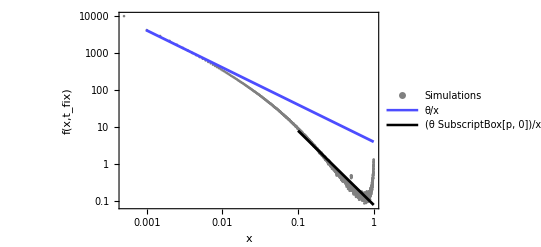

```mathematica
N1=1000;
mu=10^-7;
L=10000;
theta=4 N1 mu L;s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/average_data_high_CI_paper_s_0.1.txt"];

datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x21s};

a1s=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","\!\(\*
StyleBox[\"f\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\"(\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\"x\",\nFontSlant->\"Italic\"]\)\!\(\*
StyleBox[\",\",\nFontSlant->\"Italic\"]\)\!\(\*SubscriptBox[
StyleBox[\"t\",\nFontSlant->\"Italic\"], \(fix\)]\)\!\(\*
StyleBox[\")\",\nFontSlant->\"Italic\"]\)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray},PlotLegends->{"Simulations","Diffusion"}];
a2s=LogLogPlot[theta/x,{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{"\!\(\*FractionBox[\(θ\), \(x\)]\)","Diffusion"}];
a3s=LogLogPlot[theta/(50 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{"\!\(\*FractionBox[\(θ\\\  \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)","Diffusion"}];

Show[a1s,a2s,a3s,PlotRange->All]
```

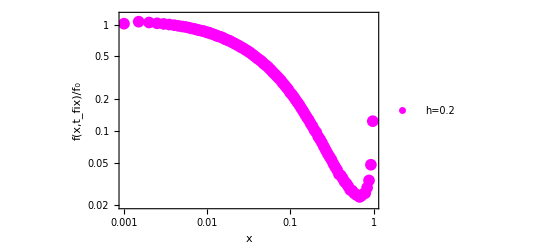

```mathematica
N1=1000;
mu=10^-7;
L=10000;
theta=4 N1 mu L;
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/average_data_high_CI_paper_s_0.1.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1s=Transpose@{x11s,x11s x21s/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.02,1.2}}, PlotMarkers->{"●",12}];

(*Show both plots*)
Show[a1sCombined]
```

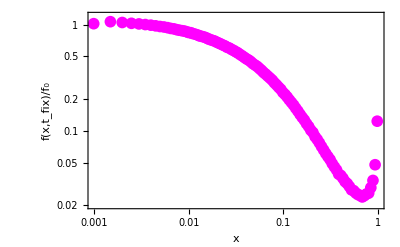
```mathematica
a1=-Graphics-;
```

```mathematica
N1=1000;
mu=10^-7;
L=10000;
theta=4 N1 mu L
```

4

```mathematica
Quit[]
```

```mathematica
N1 = 1000;
mu = 10^-7;
L = 10/100 1000;
theta = 4 N1 mu L; 
h = 0.5;

s=0.1;
b = LogLogPlot[{  x/(4 2 (* this should be of neutral theta *)) (theta ⅇ^(4 N1 s ((1-2 h)x^2 + 2 h x )) ∫_x^1 ⅇ^(-4 N1 s ( (1-2 h) y^2 + 2 h y ))ⅆy)/(x (1-x) ∫_0^1 ⅇ^(-4 N1 s ( (1- 2h) y^2 + 2 h y))ⅆy) }, {x,0.4,0.99}, FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Dashed,Magenta},PlotLegends->{"1/(x (1 - x))"}];
```

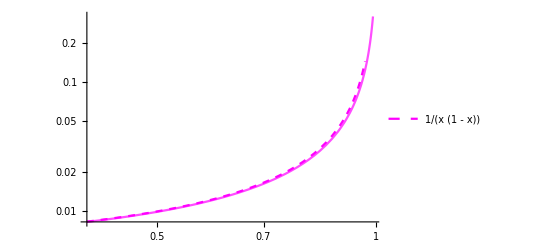

```mathematica
Show[a2,b]
```

```mathematica
Quit[]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

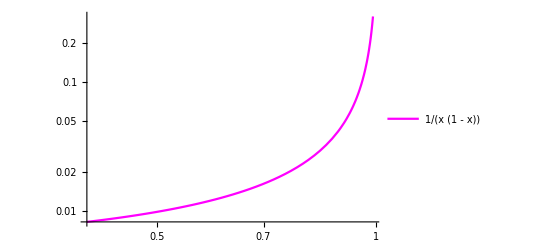

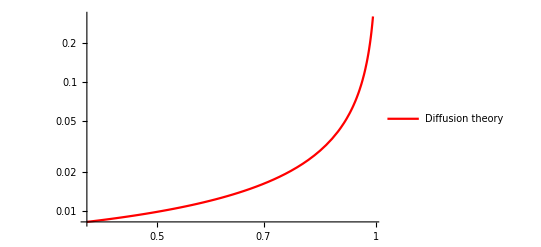

```mathematica
N1 = 1000;
mu = 10^-7;
L = 10/100 1000;
theta = 4 N1 mu L; 
h = 0.5;


b = LogLogPlot[{1/2  x/4. NIntegrate[ 10 Exp[-10 s] (theta ⅇ^(2 N1 s ((1-2 h)x^2 + 2 h x )) ∫_x^1 ⅇ^(-2 N1 s ( (1-2 h) y^2 + 2 h y ))ⅆy)/(x (1-x) ∫_0^1 ⅇ^(-2 N1 s ( (1- 2h) y^2 + 2 h y))ⅆy), {s,0,Infinity}] }, {x,0.4,0.99}, FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta},PlotLegends->{"1/(x (1 - x))"}]
```

```mathematica
N1 = 1000;
mu = 10^-7;
L = 10/100 1000;
theta = 4 N1 mu L
```

1/25

```mathematica
N1 = 1000;
mu = 10^-7;
L = 10/100 1000;
theta = 4 N1 mu L; 
h = 0.5;


b = LogLogPlot[{1/2  x/4. NIntegrate[ 10 Exp[-10 s] (theta ⅇ^(2 N1 s ((1-2 h)x^2 + 2 h x )) ∫_x^1 ⅇ^(-2 N1 s ( (1-2 h) y^2 + 2 h y ))ⅆy)/(x (1-x) ∫_0^1 ⅇ^(-2 N1 s ( (1- 2h) y^2 + 2 h y))ⅆy), {s,0,Infinity}] }, {x,0.4,0.99}, PlotStyle->Lighter[Magenta, 0.3]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-Graphics-

```mathematica
a2=-Graphics-;
```

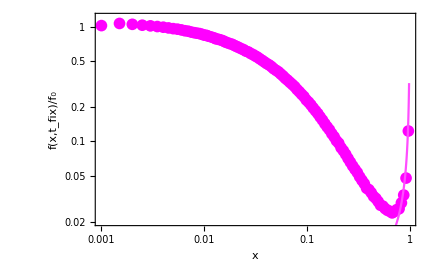

```mathematica
Show[a1,a2]
```

```mathematica
f2=-Graphics-;
```

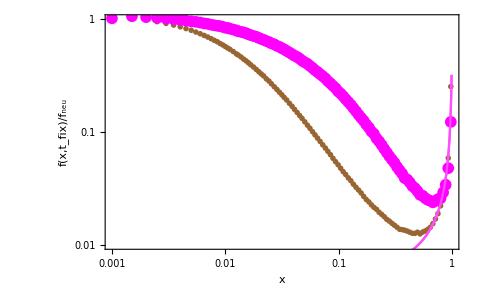

```mathematica
Show[f1,f2]
```

```mathematica
N1=1000;
mu=10^-7;
L=10000;
theta=4 N1 mu L;
```

```mathematica
theta
```

4

```mathematica
2 N1 2 h s
```

100.

```mathematica
Quit[]
```

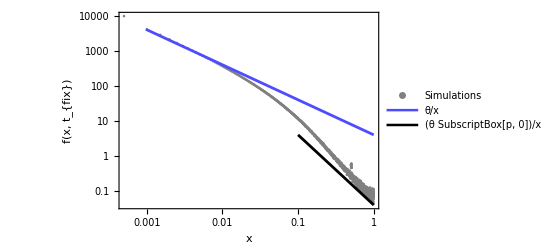

```mathematica
N1=1000;
mu=10^-7;
L=10000;
theta=4 N1 mu L;


s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/average_data_No_CI_paper.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];


x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];
Data1s=Transpose@{x11s,x21s};

a1s=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x",Style["f(x, t_{fix})",Italic,Medium]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray},PlotLegends->Placed[{"Simulations"},{0.2,0.4}]];

a2s=LogLogPlot[theta/x,{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->Placed[{"\!\(\*FractionBox[\(θ\), \(x\)]\)"},{0.2,0.3}]];

a3s=LogLogPlot[theta/(100 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->Placed[{"\!\(\*FractionBox[\(θ\ \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)"},{0.2,0.2}]];

Show[a1s,a2s,a3s,PlotRange->All]
```

```mathematica
N1=1000;
mu=10^-7;
L=10000;
theta=4 N1 mu L
```

4

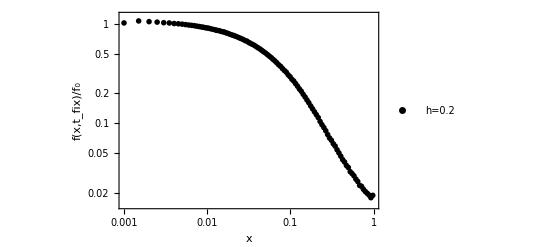

```mathematica
N1=1000;
mu=10^-7;
L=10000;
theta=4 N1 mu L;
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/average_data_No_CI_paper.txt"];
datas1s=ReadList[s1s,{Number,Number}];
Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];

Data1s=Transpose@{x11s,x11s x21s/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Black},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.015,1.2}}, PlotMarkers->{"✶",12}];

(*Show both plots*)
Show[a1sCombined]
```

```mathematica
f1=-Graphics-;
```

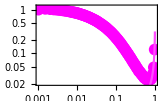
```mathematica
f2=-Graphics-;
```

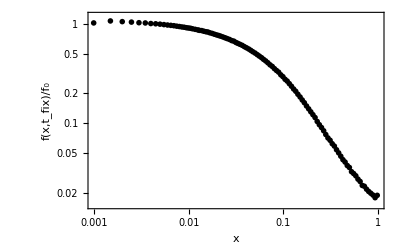
```mathematica
f3=-Graphics-;
```

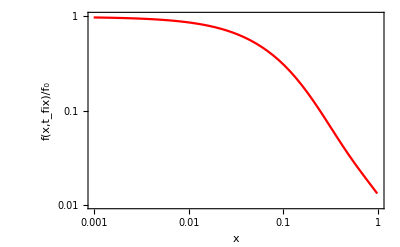
```mathematica
d1=-Graphics-;
```

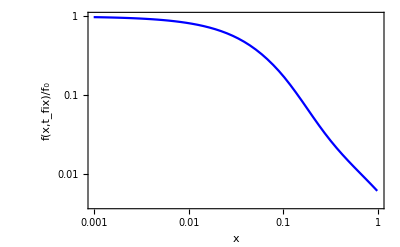
```mathematica
d1=-Graphics-;
```

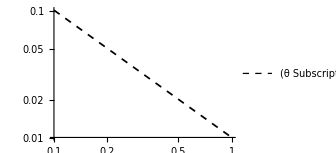
```mathematica
c1=-Graphics-;
```

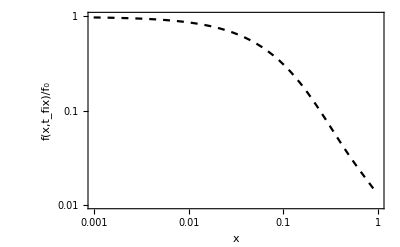
```mathematica
c2=-Graphics-;
```

```mathematica
Show[f1,f2,f3,d1,c1]
```

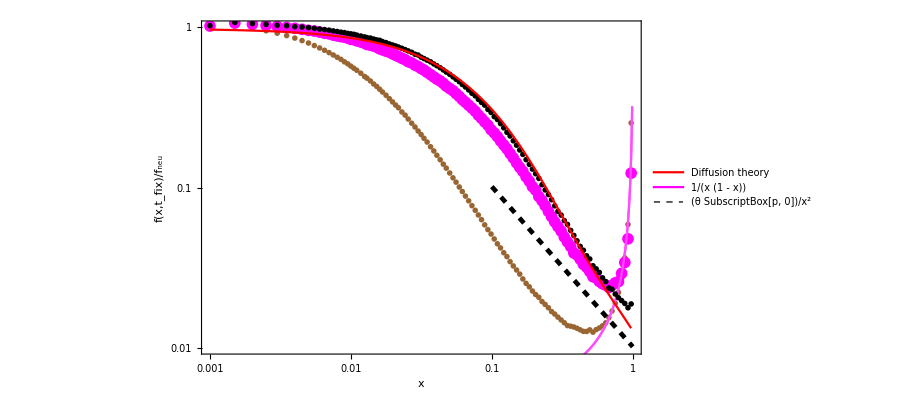

```mathematica
Show[f1,f2,f3,d1,c2]
```

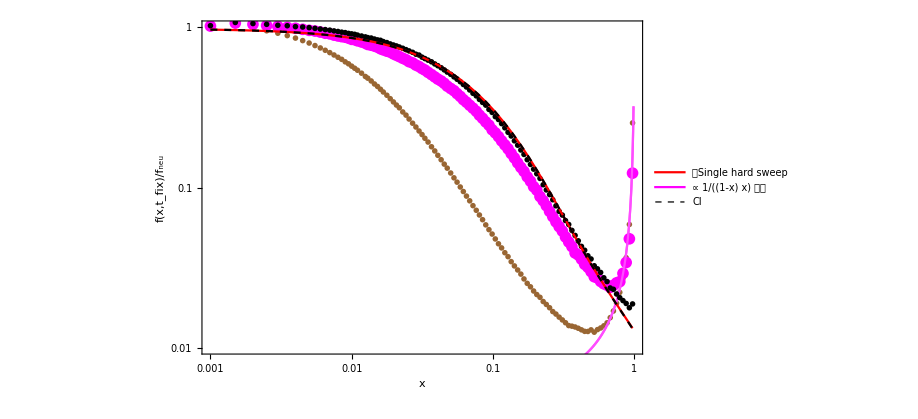

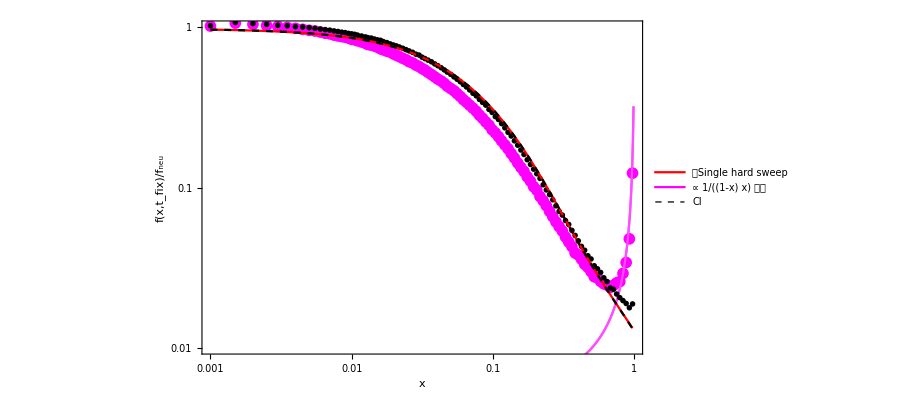
```mathematica
a1=-Graphics-;
```

```mathematica
Show[a1sCombined,a1]
```

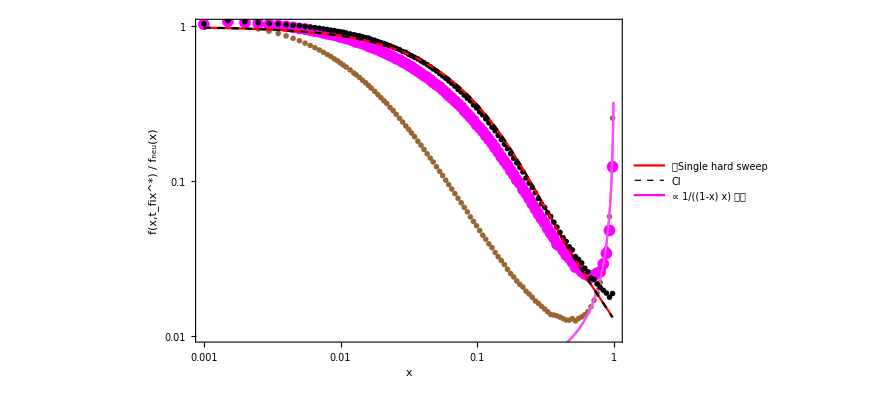

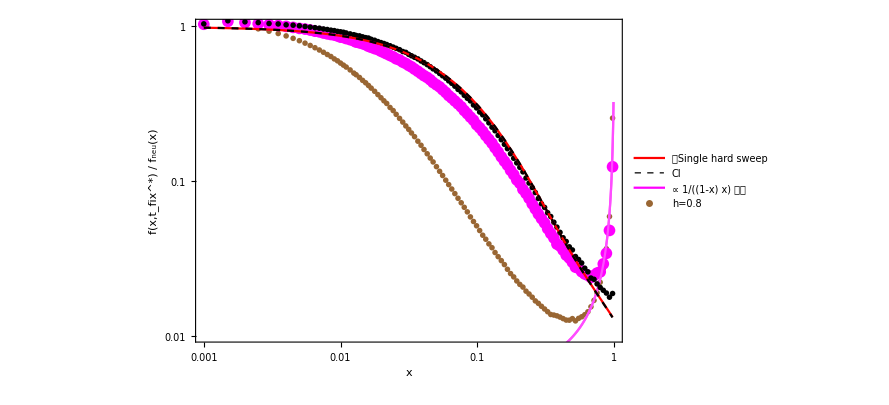

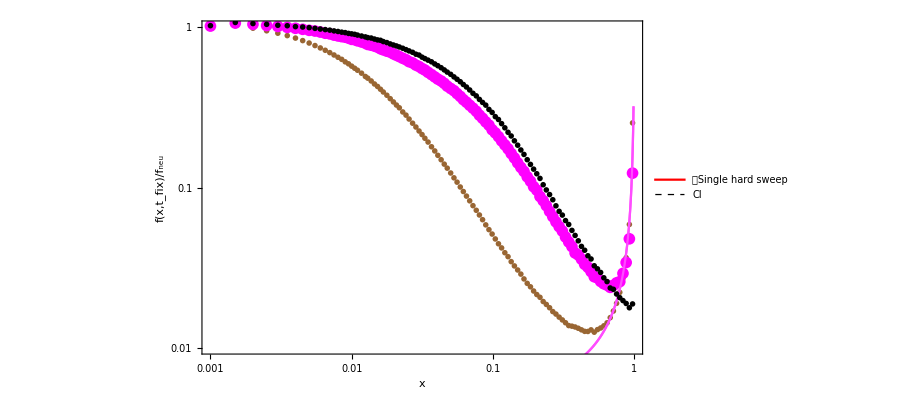
```mathematica
a1=-Graphics-;
```

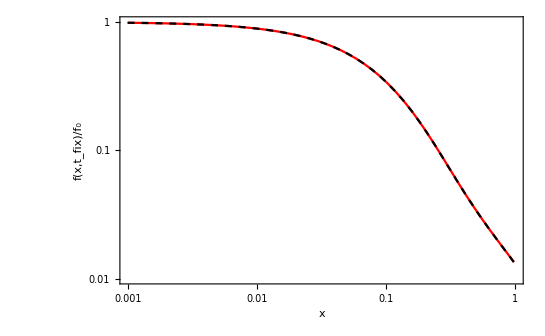
```mathematica
a2=-Graphics-;
```

```mathematica
Show[a1,a2]
```

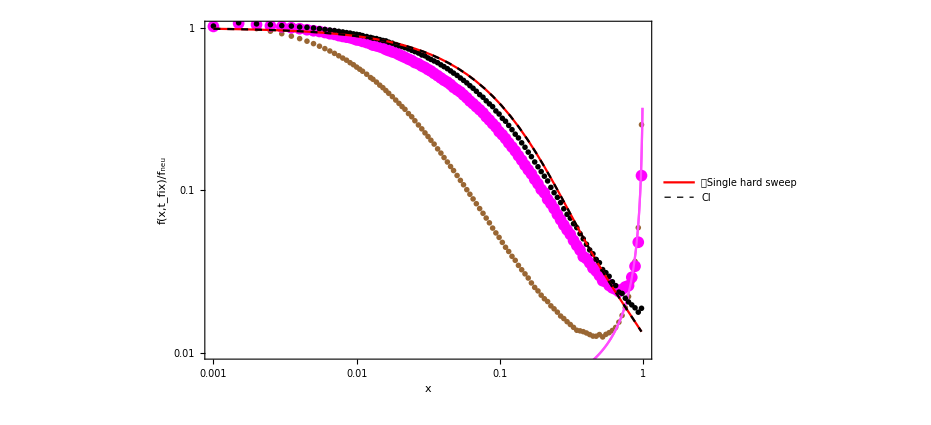

```mathematica
1/(x(1-x))
```

1/((1-x) x)

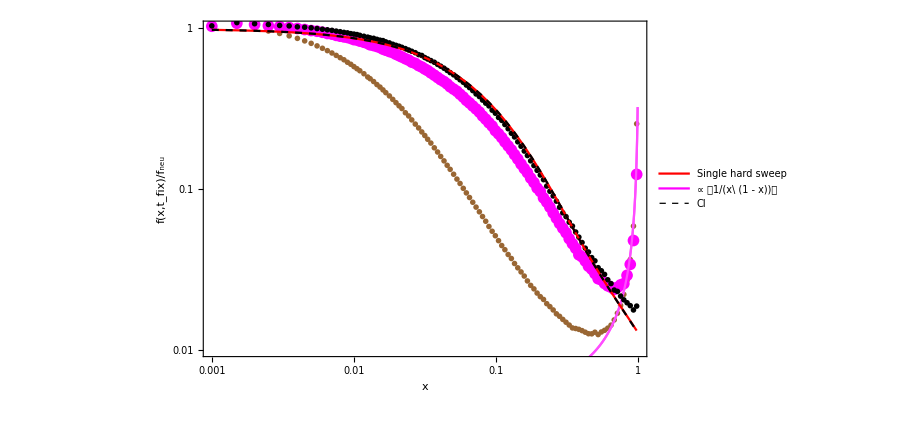

```mathematica
∝]●●★♣
```

```mathematica
Quit[]
```

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

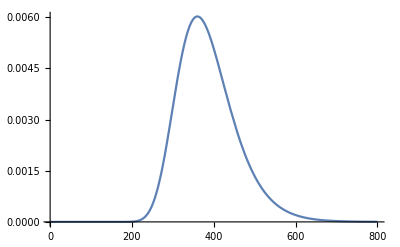

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
N1=1000;
s0=0.05;
h=0.5;
x0=1/(2 N1);


si[t_]:=s0;


taui[t_]:=taui[t]=h*NIntegrate[si[t1],{t1,0,t}];


pf1=2/(1+NIntegrate[Exp[-taui[t]],{t,0,Infinity}]);

C1=2 N1 pf1;

B[Te_]:=B[Te]=(2 N1)/NIntegrate[Exp[(1-h)/h taui[t]],{t,0,Te}];


pdfgenh[Te_]:=pdfgenh[Te]=h/(1-h) (C1 B[Te]^2)/(2 N1) Exp[(1-h)/h taui[Te]]*NIntegrate[q^(-(h/(1-h))) Exp[-B[Te] q] Exp[-C1 q^(-h/(1-h))],{q,0,Infinity},MaxRecursion->20];

a3=Plot[pdfgenh[t],{t,1,800},PlotRange->All,PlotPoints->50]




timePoints=Range[1,800,1];

weightValues=pdfgenh/@timePoints;

Datatfix=Transpose[{timePoints,weightValues}];
```

```mathematica
Datatfix
```

```mathematica
Datatfix={{1,0.},{2,5.950509082251953*^-265},{3,1.0197819642623125*^-214},{4,1.2705023283868593*^-184},{5,5.5760189681749226*^-164},{6,1.1522001592661253*^-148},{7,1.059611228901847*^-136},{8,5.220547717856088*^-127},{9,6.120119420965296*^-119},{10,4.437692752429766*^-112},{11,3.7905300587297575*^-106},{12,5.996334594187069*^-101},{13,2.439687373604125*^-96},{14,3.261529706865674*^-92},{15,1.7271724811594246*^-88},{16,4.1905420683688476*^-85},{17,5.227002689918575*^-82},{18,3.676884209857814*^-79},{19,1.5728001660169622*^-76},{20,4.3529178759186874*^-74},{21,8.207728818318017*^-72},{22,1.101115409475718*^-69},{23,1.0903344306385658*^-67},{24,8.222730659733712*^-66},{25,4.8517759286269015*^-64},{26,2.292622255157713*^-62},{27,8.85350007245268*^-61},{28,2.8441286982423345*^-59},{29,7.719793185356623*^-58},{30,1.7949993356517437*^-56},{31,3.619345075892118*^-55},{32,6.397757384118833*^-54},{33,1.0011106565549944*^-52},{34,1.3988892617643993*^-51},{35,1.759315684377865*^-50},{36,2.00560261685395*^-49},{37,2.0858242109780372*^-48},{38,1.9905690165432987*^-47},{39,1.752475974525558*^-46},{40,1.43024302627503*^-45},{41,1.0868742509329757*^-44},{42,7.721994905492328*^-44},{43,5.148569034939529*^-43},{44,3.232571073670603*^-42},{45,1.9173274526276326*^-41},{46,1.0774796390233866*^-40},{47,5.752677897583946*^-40},{48,2.9253472765750313*^-39},{49,1.420207354557322*^-38},{50,6.596946612843216*^-38},{51,2.93789707529313*^-37},{52,1.2567799231448034*^-36},{53,5.173491339969966*^-36},{54,2.0527376406805494*^-35},{55,7.8629664730539*^-35},{56,2.9119168154624162*^-34},{57,1.0440202660260947*^-33},{58,3.628596775906807*^-33},{59,1.2240465313323779*^-32},{60,4.012230513090643*^-32},{61,1.2793040008130078*^-31},{62,3.9719768667951294*^-31},{63,1.202003307556008*^-30},{64,3.548697908715242*^-30},{65,1.0229967840745767*^-29},{66,2.881902558101911*^-29},{67,7.94006005343176*^-29},{68,2.141067731011299*^-28},{69,5.654651936487812*^-28},{70,1.4636661338689133*^-27},{71,3.715495174841928*^-27},{72,9.255388814631628*^-27},{73,2.263749602255508*^-26},{74,5.439497376307455*^-26},{75,1.2847418552669109*^-25},{76,2.98414224557105*^-25},{77,6.81992998672481*^-25},{78,1.534257251751335*^-24},{79,3.39912307577058*^-24},{80,7.419429492034749*^-24},{81,1.5961948102352741*^-23},{82,3.3859665207733074*^-23},{83,7.084734803960819*^-23},{84,1.4627329108889296*^-22},{85,2.980966926096287*^-22},{86,5.99852338110961*^-22},{87,1.1922449746850411*^-21},{88,2.341284723065696*^-21},{89,4.544009375550689*^-21},{90,8.7185529587561*^-21},{91,1.6542047369322004*^-20},{92,3.104480603491163*^-20},{93,5.764406431332703*^-20},{94,1.0592376912322236*^-19},{95,1.9266773342778314*^-19},{96,3.469774887143731*^-19},{97,6.188238118195553*^-19},{98,1.0931999125631937*^-18},{99,1.9133278726214917*^-18},{100,3.3183629433374566*^-18},{101,5.704108196632312*^-18},{102,9.719925476900352*^-18},{103,1.642210629655581*^-17},{104,2.751455469597451*^-17},{105,4.572339155618802*^-17},{106,7.537530214877718*^-17},{107,1.2328339321959052*^-16},{108,2.0009355957099748*^-16},{109,3.223152145521798*^-16},{110,5.153614262353275*^-16},{111,8.180669170568393*^-16},{112,1.2893541450146468*^-15},{113,2.017999453753693*^-15},{114,3.136841959724647*^-15},{115,4.843315706444988*^-15},{116,7.428920953728071*^-15},{117,1.1321248897411863*^-14},{118,1.7143520608017932*^-14},{119,2.5798404791713705*^-14},{120,3.858527958610083*^-14},{121,5.736327778719702*^-14},{122,8.477662515221142*^-14},{123,1.2456422579123674*^-13},{124,1.8198251222727984*^-13},{125,2.6437968574629587*^-13},{126,3.819711456651933*^-13},{127,5.488807767258589*^-13},{128,7.845315955288071*^-13},{129,1.1154929650294755*^-12},{130,1.5779212595826137*^-12},{131,2.2207677911461515*^-12},{132,3.109973497382138*^-12},{133,4.333926111221825*^-12},{134,6.010524310650543*^-12},{135,8.296277030357203*^-12},{136,1.1397967368797607*^-11},{137,1.5587532362154537*^-11},{138,2.122095570611857*^-11},{139,2.8762144010321188*^-11},{140,3.8812962940920206*^-11},{141,5.215085058439987*^-11},{142,6.977571015571927*^-11},{143,9.296811266231683*^-11},{144,1.2336122154067368*^-10},{145,1.6302930146190986*^-10},{146,2.1459616252122148*^-10},{147,2.8136744688525693*^-10},{148,3.674914313491616*^-10},{149,4.781535556048008*^-10},{150,6.198108994981789*^-10},{151,8.004736460808394*^-10},{152,1.0300416180025653*^-9},{153,1.3207050925705373*^-9},{154,1.6874203297155834*^-9},{155,2.148471584815197*^-9},{156,2.7261328252584042*^-9},{157,3.447443923994003*^-9},{158,4.3451177660982786*^-9},{159,5.458596453262606*^-9},{160,6.835276655434332*^-9},{161,8.531926074077718*^-9},{162,1.0616314985039856*^-8},{163,1.3169088871294891*^-8},{164,1.628591022993545*^-8},{165,2.0079899716851854*^-8},{166,2.4684408850307453*^-8},{167,3.0256158495577696*^-8},{168,3.697877928540686*^-8},{169,4.506679189854075*^-8},{170,5.4770066785179426*^-8},{171,6.63788043259105*^-8},{172,8.022907759870005*^-8},{173,9.670898080027112*^-8},{174,1.1626542689776473*^-7},{175,1.3941163822005674*^-7},{176,1.6673537338702216*^-7},{177,1.9890793317128848*^-7},{178,2.366939865439213*^-7},{179,2.809622562340254*^-7},{180,3.326971005470306*^-7},{181,3.93011025071619*^-7},{182,4.631581538723435*^-7},{183,5.445486851934841*^-7},{184,6.387643514374275*^-7},{185,7.475748969181853*^-7},{186,8.729555801481476*^-7},{187,1.0171056997861012*^-6},{188,1.1824681350554572*^-6},{189,1.3717498824495435*^-6},{190,1.5879435608204862*^-6},{191,1.8343498467199976*^-6},{192,2.1146007909778476*^-6},{193,2.432683956208445*^-6},{194,2.792967303210749*^-6},{195,3.200224742198759*^-6},{196,3.659662252561206*^-6},{197,4.1769444625089485*^-6},{198,4.758221567643802*^-6},{199,5.410156455295588*^-6},{200,6.139951889553536*^-6},{201,6.955377600396398*^-6},{202,7.864797109337064*^-6},{203,8.877194113678571*^-6},{204,0.000010002198241964331},{205,0.000011250109984925331},{206,0.000012631924596332553},{207,0.000014159354760233728},{208,0.000015844851799172605},{209,0.000017701625215580637},{210,0.000019743660339389127},{211,0.000021985733863112725},{212,0.000024443427043985392},{213,0.000027133136356522095},{214,0.000030072081383039037},{215,0.00003327830973630203},{216,0.00003677069881715221},{217,0.000040568954218806044},{218,0.000044693604603231054},{219,0.00004916599288640241},{220,0.00005400826358673248},{221,0.000059243346205618835},{222,0.00006489493452900884},{223,0.00007098746175767741},{224,0.00007754607139478766},{225,0.00008459658384523574},{226,0.00009216545869028733},{227,0.00010027975265321534},{228,0.00010896707326068764},{229,0.00011825552825822004},{230,0.00012817367084874478},{231,0.00013875044085317285},{232,0.0001500151019163771},{233,0.00016199717490711607},{234,0.00017472636768495775},{235,0.00018823250143113607},{236,0.0002025454337633637},{237,0.0002176949788726889},{238,0.00023371082497220506},{239,0.0002506224492599217},{240,0.00026845903082920976},{241,0.00028724936171120493},{242,0.0003070217564599845},{243,0.00032780396059872637},{244,0.0003496230582859305},{245,0.00037250537956601563},{246,0.0003964764075754603},{247,0.0004215606860804016},{248,0.0004477817277242041},{249,0.0004751619233640384},{250,0.0005037224528736499},{251,0.0005334831977653188},{252,0.0005644626561435395},{253,0.0005966778599164975},{254,0.0006301442953321805},{255,0.000664875826472229},{256,0.0007008846224374632},{257,0.0007381810884064269},{258,0.0007767738008771735},{259,0.0008166694473626311},{260,0.000857872770797719},{261,0.0009003865067735077},{262,0.0009442113986201699},{263,0.0009893460361274575},{264,0.001035786942031683},{265,0.0010835284824794462},{266,0.0011325628559280608},{267,0.0011828800757987513},{268,0.0012344679590602621},{269,0.0012873121207852163},{270,0.0013413959746966333},{271,0.0013967007396974138},{272,0.0014532054523513829},{273,0.001510886985260793},{274,0.0015697200712620923},{275,0.001629677333339532},{276,0.0016907293201346841},{277,0.0017528445469094872},{278,0.0018159895418009726},{279,0.0018801288971874535},{280,0.001945225325968867},{281,0.002011239722547956},{282,0.0020781312283394545},{283,0.002145857301180565},{284,0.0022143737895908102},{285,0.002283635009406626},{286,0.0023535938251528833},{287,0.002424201733847993},{288,0.0024954089518191714},{289,0.002567164504474533},{290,0.002639416317004655},{291,0.0027121113094339244},{292,0.0027851954912315284},{293,0.0028586140582774547},{294,0.002932311490745426},{295,0.0030062316517833775},{296,0.0030803178868358417},{297,0.003154513122373841},{298,0.003228759966596306},{299,0.0033030008070884746},{300,0.0033771779099120657},{301,0.003451233517025029},{302,0.0035251099427306277},{303,0.00359874966878174},{304,0.003672095437912187},{305,0.003745090345577914},{306,0.0038176779297022624},{307,0.0038898022582313455},{308,0.003961408014317845},{309,0.0040324405789637805},{310,0.004102846110965645},{311,0.004172571624017847},{312,0.0042415650608433764},{313,0.004309775364233437},{314,0.00437715254489058},{315,0.004443647745982614},{316,0.0045092133043272324},{317,0.0045738028081396395},{318,0.004637371151287686},{319,0.004699874584010996},{320,0.0047612707600721196},{321,0.004821518780319157},{322,0.0048805792326501625},{323,0.004938414228380189},{324,0.0049949874350220785},{325,0.005050264105501582},{326,0.005104211103836998},{327,0.005156796927321907},{328,0.005207991725258216},{329,0.005257767314294437},{330,0.005306097190431229},{331,0.005352956537763602},{332,0.005398322234034867},{333,0.0054421728530837845},{334,0.005484488664271312},{335,0.005525251628978482},{336,0.0055644453942710215},{337,0.005602055283830441},{338,0.0056380682862546},{339,0.005672473040833642},{340,0.005705259820909891},{341,0.005736420514932059},{342,0.005765948605316105},{343,0.00579383914522608},{344,0.0058200887333891395},{345,0.005844695487059617},{346,0.005867659013246887},{347,0.005888980378321684},{348,0.005908662076115013},{349,0.0059267079946229186},{350,0.00594312338142922},{351,0.005957914807957077},{352,0.005971090132658308},{353,0.005982658463248015},{354,0.0059926301180894615},{355,0.006001016586832273},{356,0.006007830490404353},{357,0.006013085540455522},{358,0.006016796498347766},{359,0.006018979133784673},{360,0.006019650183090295},{361,0.00601882730777492},{362,0.006016529051817958},{363,0.00601277480050079},{364,0.006007584738115384},{365,0.006000979806269991},{366,0.0059929817057181025},{367,0.005983612638025071},{368,0.00597289569862473},{369,0.005960854402177177},{370,0.005947512859432621},{371,0.005932895694165106},{372,0.005917028004055534},{373,0.005899935322166205},{374,0.005881643579049927},{375,0.005862179065533847},{376,0.005841568396214891},{377,0.005819838473700503},{378,0.005797016453625826},{379,0.005773129710475051},{380,0.005748205804232144},{381,0.005722272447883409},{382,0.005695357475791595},{383,0.005667488812958524},{384,0.005638694445191256},{385,0.005609002390183595},{386,0.005578440669523379},{387,0.00554703728163291},{388,0.005514820175648429},{389,0.0054818172262420545},{390,0.005448056209388008},{391,0.005413564779072886},{392,0.00537837044494806},{393,0.005342500550920805},{394,0.005305982254678801},{395,0.005268842508141726},{396,0.005231108038831677},{397,0.0051928053321534315},{398,0.00515396061457394},{399,0.005114599837689555},{400,0.005074748663168302},{401,0.005034432448553728},{402,0.004993676233915676},{403,0.004952504729332982},{404,0.004910942303191808},{405,0.004869012971283182},{406,0.0048267403866823115},{407,0.004784147830391913},{408,0.0047412582027313785},{409,0.004698094015452984},{410,0.004654677384566203},{411,0.004611030023850785},{412,0.004567173239039036},{413,0.004523127922647562},{414,0.004478914549438626},{415,0.004434553172491065},{416,0.00439006341986086},{417,0.004345464491811169},{418,0.004300775158591902},{419,0.004256013758748902},{420,0.004211198197942811},{421,0.004166345948257932},{422,0.0041214740479816065},{423,0.004076599101834572},{424,0.0040317372816332745},{425,0.003986904327365207},{426,0.00394211554865853},{427,0.0038973858266276766},{428,0.003852729616076863},{429,0.0038081609480436324},{430,0.003763693432665144},{431,0.003719340262350016},{432,0.0036751142152389943},{433,0.003631027658938158},{434,0.003587092554508542},{435,0.0035433204606966627},{436,0.003499722538390715},{437,0.003456309555287599},{438,0.0034130918907563385},{439,0.003370079540883957},{440,0.003327282123690055},{441,0.003284708884497066},{442,0.003242368701443241},{443,0.003200270091126064},{444,0.003158421221688348},{445,0.003116829892197737},{446,0.003075503574959128},{447,0.0030344493991963156},{448,0.0029936741382182823},{449,0.002953184305118052},{450,0.0029129860338807834},{451,0.00287308516382326},{452,0.002833487227536838},{453,0.0027941974572420663},{454,0.002755220791163744},{455,0.002716561879918556},{456,0.002678225092908079},{457,0.0026402145247099236},{458,0.002602534001460479},{459,0.002565187087222768},{460,0.002528177090333434},{461,0.0024915070697231006},{462,0.002455179841204665},{463,0.002419197983724415},{464,0.002383563845571129},{465,0.0023482795505385913},{466,0.002313347004037237},{467,0.002278767899150956},{468,0.0022445437226351994},{469,0.0022106757608529952},{470,0.0021771651056455275},{471,0.002144012660134274},{472,0.002111219144451898},{473,0.0020787851013993},{474,0.002046710902026466},{475,0.002014996751134916},{476,0.001983642692699822},{477,0.0019526486152099509},{478,0.0019220142569238703},{479,0.0018917392110409446},{480,0.0018618229307858863},{481,0.0018322647344057254},{482,0.0018030638100782566},{483,0.0017742192207311396},{484,0.0017457299087709677},{485,0.0017175947007218107},{486,0.0016898123117727681},{487,0.0016623813502342631},{488,0.001635300321902925},{489,0.0016085676343349546},{490,0.0015821816010280325},{491,0.0015561404455119025},{492,0.0015304423053478797},{493,0.001505085236037559},{494,0.0014800672148411595},{495,0.001455386144505949},{496,0.0014310398569053354},{497,0.0014070261165892053},{498,0.0013833426242462086},{499,0.0013599870200787405},{500,0.001336956887091414},{501,0.0013142497542938498},{502,0.0012918630998187425},{503,0.0012697943539561067},{504,0.0012480409021047058},{505,0.0012266000876417142},{506,0.00120546921471162},{507,0.001184645550935537},{508,0.0011641263300420034},{509,0.0011439087544204115},{510,0.0011239899975982628},{511,0.0011043672066434343},{512,0.0010850375044926487},{513,0.001065997992207397},{514,0.0010472457511585464},{515,0.0010287778451408757},{516,0.0010105913224188233},{517,0.0009926832177047033},{518,0.0009750505540706775},{519,0.0009576903447957631},{520,0.0009405995951491709},{521,0.0009237753041112393},{522,0.0009072144660320615},{523,0.0008909140722376127},{524,0.0008748711125589545},{525,0.0008590825768286965},{526,0.0008435454563030373},{527,0.0008282567450364232},{528,0.0008132134412014654},{529,0.0007984125483566146},{530,0.0007838510766627924},{531,0.0007695260440502427},{532,0.0007554344773367849},{533,0.0007415734132996325},{534,0.000727939899696514},{535,0.0007145309962500572},{536,0.0007013437755810911},{537,0.0006883753241022284},{538,0.0006756227428809077},{539,0.0006630831483940341},{540,0.0006507536734106763},{541,0.0006386314676155603},{542,0.0006267136983601391},{543,0.0006149975513116316},{544,0.0006034802310779471},{545,0.0005921589617984564},{546,0.0005810309877016682},{547,0.0005700935736307373},{548,0.0005593440055378174},{549,0.0005487795909481852},{550,0.0005383976593950613},{551,0.0005281955628260637},{552,0.0005181706759821739},{553,0.0005083203967501021},{554,0.0004986421464888944},{555,0.0004891333703316389},{556,0.0004797915374630751},{557,0.00047061414137391177},{558,0.00046159870009265},{559,0.0004527427563956431},{560,0.00044404387799619385},{561,0.0004354996577133719},{562,0.0004271077136213026},{563,0.00041886568917962747},{564,0.00041077125334580423},{565,0.0004028221006699429},{566,0.0003950159513728212},{567,0.000387350551407722},{568,0.00037982367250951796},{569,0.0003724331122136173},{570,0.00036517669389301335},{571,0.00035805226674748346},{572,0.0003510577057970624},{573,0.0003441909118592817},{574,0.0003374498115142444},{575,0.00033083235705804636},{576,0.0003243365264486532},{577,0.00031796032318808003},{578,0.00031170177643782213},{579,0.0003055589405751268},{580,0.00029952989543806884},{581,0.0002936127460498697},{582,0.00028780562253786547},{583,0.0002821066800156081},{584,0.0002765140984318757},{585,0.000271026082463688},{586,0.00026564086135175667},{587,0.00026035668875372495},{588,0.0002551718425891507},{589,0.00025008462487200426},{590,0.00024509336154658753},{591,0.00024019640231160436},{592,0.00023539212044205562},{593,0.00023067891261089674},{594,0.00022605519868108682},{595,0.00022151942154678673},{596,0.00021707004691595352},{597,0.00021270556311733558},{598,0.00020842448089865631},{599,0.00020422533322781407},{600,0.00020010667506193823},{601,0.00019606708317095774},{602,0.00019210515590452427},{603,0.00018821951298238955},{604,0.00018440879527815483},{605,0.0001806716646013325},{606,0.0001770068034779073},{607,0.00017341291492958133},{608,0.00016988872225186775},{609,0.00016643296879120817},{610,0.00016304441772127334},{611,0.00015972185182391757},{612,0.00015646407324089326},{613,0.0001532699032863729},{614,0.00015013818219507247},{615,0.00014706776890780805},{616,0.00014405754082991444},{617,0.0001411063936258894},{618,0.0001382132409835492},{619,0.00013537701439115057},{620,0.00013259666291298974},{621,0.00012987115296556268},{622,0.00012719946809437797},{623,0.00012458060875151751},{624,0.00012201359207403219},{625,0.00011949745166324691},{626,0.00011703123736506236},{627,0.00011461401505132047},{628,0.00011224486640230877},{629,0.00010992288869717536},{630,0.00010764719456963834},{631,0.00010541691184128456},{632,0.00010323118327845363},{633,0.00010108916638508421},{634,0.0000989900331950509},{635,0.00009693297006649493},{636,0.00009491717747424668},{637,0.00009294186980516079},{638,0.00009100627515510728},{639,0.00008910963512768622},{640,0.00008725120463450915},{641,0.00008543025169762916},{642,0.00008364605725324515},{643,0.00008189791495760072},{644,0.00008018513099467814},{645,0.00007850702388514462},{646,0.00007686292429875575},{647,0.00007525217486684537},{648,0.00007367412999696367},{649,0.00007212815569121549},{650,0.00007061362936473075},{651,0.00006912993966659765},{652,0.00006767648630280496},{653,0.00006625267986159403},{654,0.00006485794163978395},{655,0.00006349170347206221},{656,0.00006215340756179457},{657,0.00006084250631512494},{658,0.000059558462171063344},{659,0.00005830074744539236},{660,0.000057068844165033235},{661,0.00005586224391000096},{662,0.000054680447656267495},{663,0.0000535229656206137},{664,0.00005238931710746373},{665,0.00005127903036993264},{666,0.00005019164241039913},{667,0.00004912669890075094},{668,0.0000480837540244523},{669,0.000047062370284644314},{670,0.00004606211840536017},{671,0.00004508257718106777},{672,0.00004412333333909993},{673,0.000043183981403993394},{674,0.00004226412356372171},{675,0.00004136336953780858},{676,0.00004048133644731335},{677,0.000039617648686670464},{678,0.00003877193779737368},{679,0.00003794384234348732},{680,0.000037133007788972157},{681,0.00003633908637681196},{682,0.00003556173700992244},{683,0.00003480062513383156},{684,0.00003405542262111109},{685,0.00003332580767097776},{686,0.0000326114646300285},{687,0.000031912084016148634},{688,0.00003122736227548296},{689,0.00003055700174254798},{690,0.000029900710521410393},{691,0.00002925820238193385},{692,0.00002862919665764649},{693,0.00002801341814521085},{694,0.000027410597005478585},{695,0.000026820468666113853},{696,0.00002624277372576551},{697,0.000025677257859772195},{698,0.000025123671727383},{699,0.000024581770880472606},{700,0.000024051315673737764},{701,0.00002353207117635394},{702,0.00002302380708507477},{703,0.000022526297638758652},{704,0.000022039321549394584},{705,0.00002156266184395936},{706,0.00002109610593404712},{707,0.000020639445384984817},{708,0.00002019247591377809},{709,0.000019754997291273023},{710,0.00001932681327706395},{711,0.000018907731533888085},{712,0.000018497563559634373},{713,0.00001809612461406327},{714,0.000017703233647848593},{715,0.00001731871323283578},{716,0.000016942389493497443},{717,0.000016574092039572074},{718,0.000016213653899866236},{719,0.000015860911457205253},{720,0.0000155157043845167},{721,0.000015177875582027825},{722,0.000014847271115562579},{723,0.000014523740155921924},{724,0.000014207134934421903},{725,0.000013897310608932325},{726,0.000013594125357328829},{727,0.00001329744017012635},{728,0.000013007118870495882},{729,0.0000127230280447182},{730,0.00001244503698870368},{731,0.00001217301765547072},{732,0.000011906844603568347},{733,0.0000116463949464275},{734,0.00001139154830262765},{735,0.000011142186747063513},{736,0.000010898194762997621},{737,0.000010659459194985212},{738,0.000010425869202657139},{739,0.000010197316215347209},{740,9.973693887550041*^-6},{741,9.754898055196607*^-6},{742,9.54082669273353*^-6},{743,9.331379870993481*^-6},{744,9.126459715843715*^-6},{745,8.925970382340025*^-6},{746,8.729817941189698*^-6},{747,8.537910487064516*^-6},{748,8.350157952827902*^-6},{749,8.166472145588074*^-6},{750,7.98676669501062*^-6},{751,7.810957017063415*^-6},{752,7.63896027844209*^-6},{753,7.470695361663599*^-6},{754,7.306082830817382*^-6},{755,7.145044897962231*^-6},{756,6.987505390158485*^-6},{757,6.833389717123932*^-6},{758,6.682624839503121*^-6},{759,6.535139237739603*^-6},{760,6.390862881540017*^-6},{761,6.249727199920577*^-6},{762,6.1116650518250734*^-6},{763,5.976610697304681*^-6},{764,5.844499769250058*^-6},{765,5.715269245665157*^-6},{766,5.58885743447599*^-6},{767,5.465203886851982*^-6},{768,5.34424949106707*^-6},{769,5.225936326831625*^-6},{770,5.1102077001454815*^-6},{771,4.997008106628024*^-6},{772,4.8862832073281176*^-6},{773,4.777979805003498*^-6},{774,4.672045820861699*^-6},{775,4.5684302717535006*^-6},{776,4.467083247811291*^-6},{777,4.367955890523822*^-6},{778,4.271000371239801*^-6},{779,4.176169870092208*^-6},{780,4.083418555335761*^-6},{781,3.992701563090089*^-6},{782,3.9039749774808525*^-6},{783,3.8171958111719416*^-6},{784,3.7323219862660943*^-6},{785,3.6493123156580796*^-6},{786,3.5681264846033493*^-6},{787,3.488725032817526*^-6},{788,3.4110693367821007*^-6},{789,3.3351215917218967*^-6},{790,3.2608447989093643*^-6},{791,3.188202740434137*^-6},{792,3.117159971628766*^-6},{793,3.0476818007827183*^-6},{794,2.979734274393185*^-6},{795,2.9132841618671976*^-6},{796,2.848298940483124*^-6},{797,2.7847467807455305*^-6},{798,2.722596531941517*^-6},{799,2.661817708032359*^-6},{800,2.6023804738194032*^-6}};
```

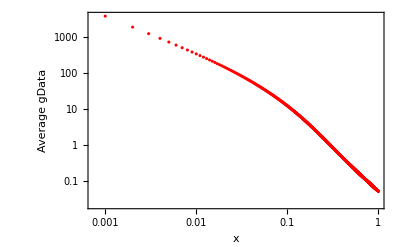

```mathematica
N1=1000;
mu=10^-7;
L=10000;
theta=4 N1 mu L;
N1=1000;s=0.05;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,4000}];



averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[Sum[Datatfix[[j,2]] G[x,Datatfix[[j,1]]]/(x*(1-x)),{j,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

```mathematica
d1=-Graphics-;
```

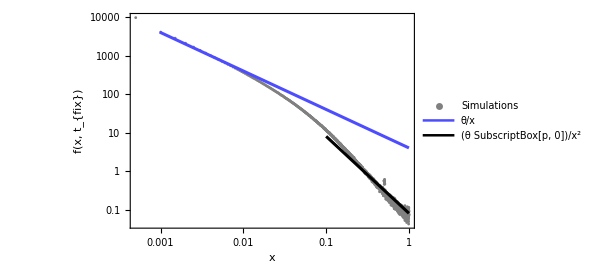
```mathematica
a1=-Graphics-;
```

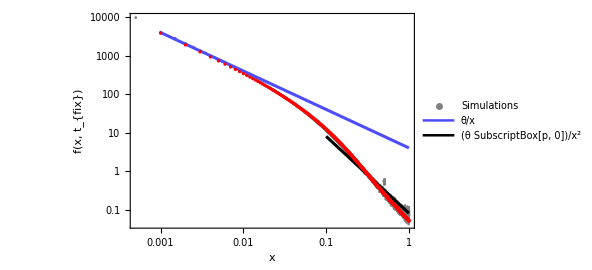

```mathematica
Show[a1,d1]
```

```mathematica
theta
```

4

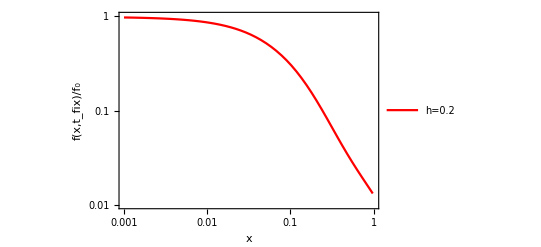

```mathematica
Data1s=Transpose@{xaxis,xaxis gData/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}, PlotMarkers->{"■",10}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.01,1}}];

(*Show both plots*)
Show[a1sInterpolated]
```

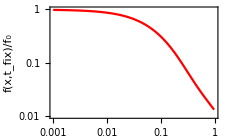
```mathematica
d1=-Graphics-;
```

```mathematica
N1=1000;
L=1000;
mu=0.005 10^-6;
s=0.05;
h=0.5
Tfix=Log[2 N1  s h]/(s h);
2 N1 mu L Tfix (2 s h)
```

0.5

0.0782405

```mathematica
N1=1000;
L=1000;
mu=10/100 10^-6;
s=0.1;
h=0.5
Tfix=Log[2 N1  s h]/(s h);
2 N1 mu L Tfix (2 s h)
```

0.5

1.84207

```mathematica
2 N1 mu L Log[2 N1  s h]/(s h) (2 s h)
```

1.84207

```mathematica
(mu 1000)/(s h) N1 Log[N1] Exp[-alpha s] (2 h s+1/alpha)
```

0.0125693

```mathematica
2 N1 2 h s Exp[-1.842068074395237]
```

31.6979

```mathematica
alpha=10; (* s mean*)
ratio=0.005;
mu=0.005 10^-7;
s=0.05;
h=0.5;
l1=(mu 1000)/(s h) N1 Log[N1] Exp[-alpha s] (2 h s+1/alpha);
2 h s Exp[-l1];
2 N1 2 h s Exp[-l1]
2 h s 2 N1
```

98.7509

100.

```mathematica
2 h s Exp[-l1]
```

0.0987509

```mathematica
2 h s
```

0.1

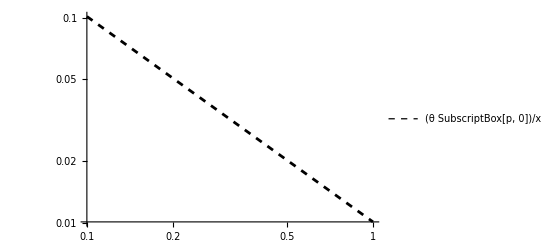

```mathematica
a3s=LogLogPlot[x /(98.75093675754654 x^2),{x,0.1,1},PlotStyle->{Black,Dashed,Thickness[0.005]},PlotLegends->Placed[{"\!\(\*FractionBox[\(θ\ \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)"},{0.2,0.2}],FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium]]
```

```mathematica
Quit[]
```

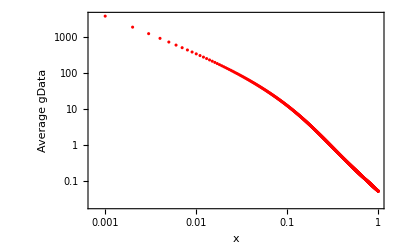

```mathematica
N1=1000;
mu=10^-7;
L=10000;
theta=4 N1 mu L;


alpha=10; (* s mean*)
ratio=0.005;
mu1=0.005 10^-7;
s=0.05;
h=0.5;
l1=(mu1 1000)/(s h) N1 Log[N1] Exp[-alpha s] (2 h s+1/alpha);

N1=1000;s=0.05;h=0.5;x0=1/(2 2 h s Exp[-l1]  N1);

(*N1=1000;s=0.05;h=0.5;x0=1/(2 2 h s N1);*)
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,1000}]; 



averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[Sum[Datatfix[[j,2]] G[x,Datatfix[[j,1]]]/(x*(1-x)),{j,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

```mathematica
a1=-Graphics-;
```

```mathematica
a2=-Graphics-;
```

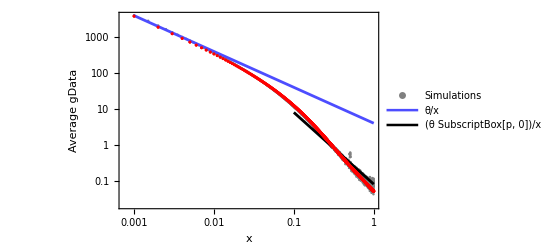

```mathematica
Show[a1,a2]
```

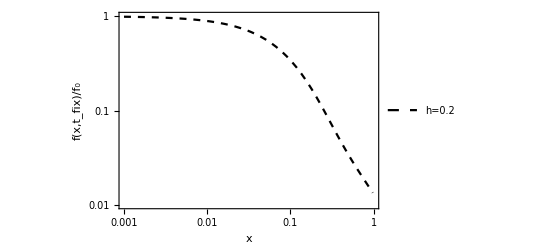

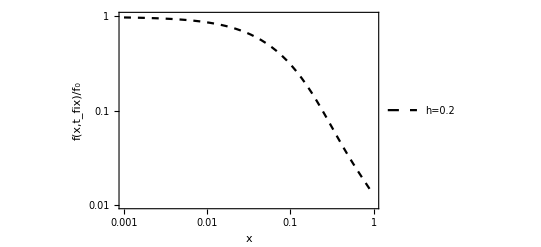

```mathematica
Data1s=Transpose@{xaxis,xaxis gData/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}, PlotMarkers->{"■",10}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Black, Dashed},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.01,1}}];

(*Show both plots*)
Show[a1sInterpolated]
```

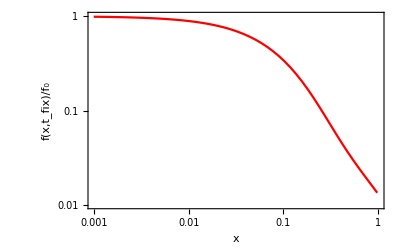
```mathematica
a1=-Graphics-;
```

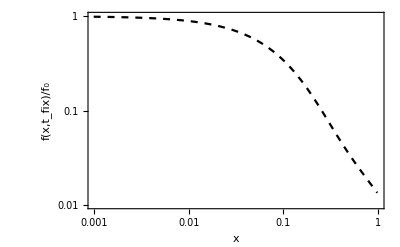
```mathematica
a2=-Graphics-;
```

```mathematica
Show[a1,a2]
```

-Graphics-

```mathematica
Sum[Datatfix[[k,2]] k,{k,1,Length[Datatfix]}]
```

385.79

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.05;h=0.5;x0=1/(2 2 s h N1);
Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h))
```

414.591

```mathematica
Quit[]
```

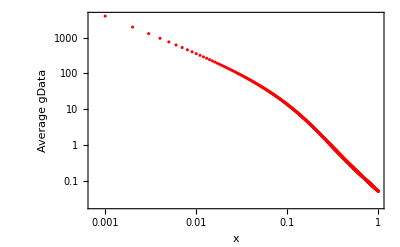

```mathematica
N1=1000;
mu=10^-7;
L=10000;
theta=4 N1 mu L;
N1=1000;s=0.05;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,4000}];


Tfix=Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h));
averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[ G[x,Tfix]/(x*(1-x)),{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

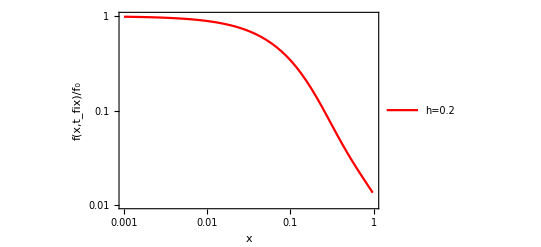

```mathematica
Data1s=Transpose@{xaxis,xaxis gData/theta};

(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.005;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.004,1}}, PlotMarkers->{"■",10}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.2"},PlotRange->{{0.001,1},{0.01,1}}];

(*Show both plots*)
Show[a1sInterpolated]
```